```mathematica
Clear["Global`*"];
(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All];

σe=Interpolation[σ[[All,{1,2}]]];
σa=Interpolation[σ[[All,{1,3}]]];
```

```mathematica
(* {NIntegrate[N2[z]/NN/.sol,{z,0,L}][[1]],σa[λs]/(σa[λs]+σe[λs])} *)
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)
λp=960;(*нм*)
λs=1064;(*нм*)
Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);
L=2;
σp12=σa[λp];σp21=σe[λp];σs12=σa[λs];σs21=σe[λs];
```

0.0121581

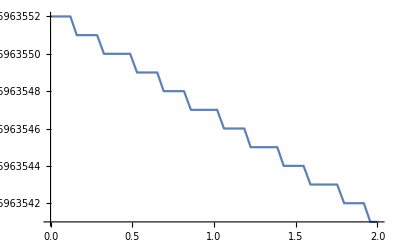

```mathematica
σa[1064]/(σa[1064]+σe[1064])
sol=NDSolve[{
0==ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),
N1[z]+N2[z]==NN, 
Ps ρs[0]==1000
},{ρs,N1,N2},{z,0,L},AccuracyGoal->Infinity];
Plot[Evaluate[{N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```